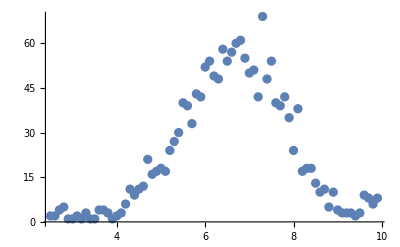

```mathematica
SetDirectory["/Users/dluntzma/Desktop/DoubleSlit-ED"];
countsnear1 = Import["20141122_single_slit_near1.csv"];
countsnear1;
ListPlot[countsnear1]
```

```mathematica
θ = (x - x0)/R;
α = π * a * Sin[θ]/λ;
β = π * d * Sin[θ]/λ; 

Subscript[i, 2] = i0/4 * (Sinc[α])^2 ;

x0= 6.6;
a = 0.085;
d = 0.343;
R = 500;
λ = .000546;
(*i0= 350;*)
```

```mathematica
fitnear1 = NonlinearModelFit[countsnear1,Subscript[i, 2],{i0}, x]
Normal[fitnear1]
```

FittedModel[56.1024 Sinc[489.076 Sin[«1» «1»]]^2]

56.1024 Sinc[489.076 Sin[1/500 (-6.8+x)]]^2

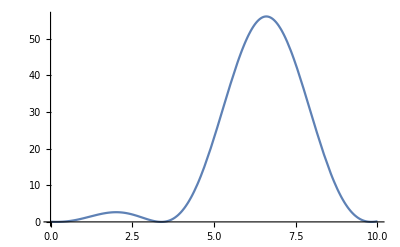

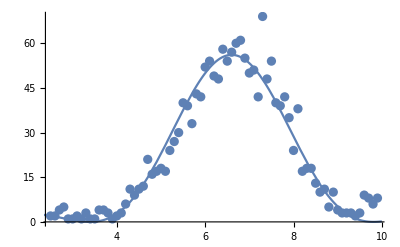

```mathematica
plotnear1=Plot[56.10237345806185*Sinc[489.0757794050044* Sin[1/500 (-6.6+x)]]^2,{x,0,10}]
Show[ListPlot[countsnear1],plotnear1]
```